```mathematica
Dhyp[n_,k_,a_]:=Dhyp[n,k,a]=Sum[Binomial[k,j] Dhyp[Floor[n/(m^(k-j))],j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
Dhyp[n_,1,a_]:=If[n<a,0,Floor[n]-a+1];Dhyp[n_,0,a_]:=1
dh[n_, k_, a_] := a^-k Dhyp[ n a^k, k, a+1]
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
Dc[n_,z_,b_]:=Expand[Sum[bins[z,a] dh[n,a,b],{a,0,30}]]
gg[n_,z_,b_] := Expand[FullSimplify[(Dc[n,z+1,b]-1)/(z+1)]]
```

```mathematica
N[Dc[100,z,2]]
```

1.+28.6045 z+42.5362 z^2+21.4569 z^3+5.62896 z^4+0.710483 z^5+0.0606425 z^6+0.00229676 z^7+0.000065633 z^8+9.94378×10^-7 z^9+4.97862×10^-9 z^10+1.22325×10^-11 z^11

```mathematica
N[gg[100,z,1]]
```

99.+100.517 z+35.1889 z^2+5.45694 z^3+0.327778 z^4+0.00972222 z^5

```mathematica
N[Dc[100,z,6]]
```

1.+28.2024 z+41.0485 z^2+22.156 z^3+6.36986 z^4+1.08782 z^5+0.124978 z^6+0.00988025 z^7+0.000579927 z^8+0.0000251671 z^9+8.52108×10^-7 z^10+2.23652×10^-8 z^11+4.67164×10^-10 z^12+7.87744×10^-12 z^13+1.06331×10^-13 z^14+1.18335×10^-15 z^15+1.05916×10^-17 z^16+8.33157×10^-20 z^17+4.49621×10^-22 z^18+2.66349×10^-24 z^19+1.01452×10^-26 z^20+2.98173×10^-29 z^21+7.56172×10^-32 z^22+2.46312×10^-34 z^23+4.11198×10^-37 z^24+2.60536×10^-40 z^25+2.95225×10^-43 z^26+2.83712×10^-46 z^27+1.94947×10^-49 z^28+9.20865×10^-53 z^29

```mathematica
Table[{n,N[Roots[ Expand[Dc[n,x,6]]==0,x]]},{n,2,16}]//TableForm
```

2 | x==-41.1436-41.3085 ⅈ||x==-41.1436+41.3085 ⅈ||x==-6.24826||x==-1.46448
3 | x==-0.756967||x==-111.626-19.2615 ⅈ||x==-111.626+19.2615 ⅈ||x==-18.9898-52.1172 ⅈ||x==-18.9898+52.1172 ⅈ||x==-5.50561-4.11081 ⅈ||x==-5.50561+4.11081 ⅈ
4 | x==-3.48734||x==-0.585923||x==-57.7458-26.6503 ⅈ||x==-57.7458+26.6503 ⅈ||x==-14.33-76.2302 ⅈ||x==-14.33+76.2302 ⅈ||x==-7.88761-9.43999 ⅈ||x==-7.88761+9.43999 ⅈ
5 | x==-403.314||x==-0.446297||x==-46.3139-281.284 ⅈ||x==-46.3139+281.284 ⅈ||x==-13.7474-10.4745 ⅈ||x==-13.7474+10.4745 ⅈ||x==-10.1821-39.2855 ⅈ||x==-10.1821+39.2855 ⅈ||x==-5.37627-1.25921 ⅈ||x==-5.37627+1.25921 ⅈ
6 | x==-43.0461||x==-29.3354||x==-0.372971||x==-289.517-833.521 ⅈ||x==-289.517+833.521 ⅈ||x==-10.5403-15.3491 ⅈ||x==-10.5403+15.3491 ⅈ||x==-4.52206-1.36965 ⅈ||x==-4.52206+1.36965 ⅈ||x==5.45645-71.2231 ⅈ||x==5.45645+71.2231 ⅈ
7 | x==-2.86963||x==-0.329815||x==-343.053-1052.15 ⅈ||x==-343.053+1052.15 ⅈ||x==-51.4753-23.254 ⅈ||x==-51.4753+23.254 ⅈ||x==-9.61663-21.5724 ⅈ||x==-9.61663+21.5724 ⅈ||x==-6.15655-5.15916 ⅈ||x==-6.15655+5.15916 ⅈ||x==12.9009-87.5627 ⅈ||x==12.9009+87.5627 ⅈ
8 | x==-855.761||x==-45.7615||x==-22.5823||x==-2.64453||x==-0.295273||x==-9.84125-24.091 ⅈ||x==-9.84125+24.091 ⅈ||x==-6.93535-4.93676 ⅈ||x==-6.93535+4.93676 ⅈ||x==2.77602-598.386 ⅈ||x==2.77602+598.386 ⅈ||x==9.52279-81.3081 ⅈ||x==9.52279+81.3081 ⅈ
9 | x==-58.854||x==-12.0168||x==-2.65441||x==-0.263642||x==-543.589-226.221 ⅈ||x==-543.589+226.221 ⅈ||x==-8.91222-23.1984 ⅈ||x==-8.91222+23.1984 ⅈ||x==-7.43134-4.84468 ⅈ||x==-7.43134+4.84468 ⅈ||x==7.07953-70.1256 ⅈ||x==7.07953+70.1256 ⅈ||x==47.2476-403.338 ⅈ||x==47.2476+403.338 ⅈ
10 | x==-89.3305||x==-4.16338||x==-3.30637||x==-0.238588||x==-232.633-202.185 ⅈ||x==-232.633+202.185 ⅈ||x==-10.2418-21.4035 ⅈ||x==-10.2418+21.4035 ⅈ||x==-8.27165-8.09041 ⅈ||x==-8.27165+8.09041 ⅈ||x==-1.99937-61.5839 ⅈ||x==-1.99937+61.5839 ⅈ||x==53.1649-232.979 ⅈ||x==53.1649+232.979 ⅈ
11 | x==-456.762||x==-92.4693||x==-35.3893||x==-2.30789||x==-0.221275||x==-334.626-1174.52 ⅈ||x==-334.626+1174.52 ⅈ||x==-8.87595-15.8768 ⅈ||x==-8.87595+15.8768 ⅈ||x==-5.02531-4.15853 ⅈ||x==-5.02531+4.15853 ⅈ||x==-4.30496-44.3813 ⅈ||x==-4.30496+44.3813 ⅈ||x==23.9073-136.838 ⅈ||x==23.9073+136.838 ⅈ
12 | x==-480.946||x==-54.7808||x==-19.2603||x==-0.203318||x==-516.457-352.808 ⅈ||x==-516.457+352.808 ⅈ||x==-7.57224-30.0774 ⅈ||x==-7.57224+30.0774 ⅈ||x==-7.36164-9.03793 ⅈ||x==-7.36164+9.03793 ⅈ||x==-3.38983-0.388817 ⅈ||x==-3.38983+0.388817 ⅈ||x==10.9064-79.4056 ⅈ||x==10.9064+79.4056 ⅈ||x==93.4699-375.305 ⅈ||x==93.4699+375.305 ⅈ
13 | x==-2.59165||x==-0.190187||x==-1318.33-1790.56 ⅈ||x==-1318.33+1790.56 ⅈ||x==-131.77-103.049 ⅈ||x==-131.77+103.049 ⅈ||x==-13.878-8.79599 ⅈ||x==-13.878+8.79599 ⅈ||x==-11.323-21.8895 ⅈ||x==-11.323+21.8895 ⅈ||x==-6.94397-1.6107 ⅈ||x==-6.94397+1.6107 ⅈ||x==-2.59521-56.0405 ⅈ||x==-2.59521+56.0405 ⅈ||x==58.2304-172.1 ⅈ||x==58.2304+172.1 ⅈ
14 | x==-610.415||x==-71.5486||x==-23.8455||x==-2.47791||x==-0.17924||x==-564.72-427.67 ⅈ||x==-564.72+427.67 ⅈ||x==-8.41084-13.1832 ⅈ||x==-8.41084+13.1832 ⅈ||x==-6.47582-37.7823 ⅈ||x==-6.47582+37.7823 ⅈ||x==-5.9453-2.02963 ⅈ||x==-5.9453+2.02963 ⅈ||x==18.3656-93.7154 ⅈ||x==18.3656+93.7154 ⅈ||x==122.419-430.78 ⅈ||x==122.419+430.78 ⅈ
15 | x==-694.591||x==-119.408||x==-95.0493||x==-2.33376||x==-0.169764||x==-366.951-1552.53 ⅈ||x==-366.951+1552.53 ⅈ||x==-9.08133-26.2288 ⅈ||x==-9.08133+26.2288 ⅈ||x==-8.12635-10.8976 ⅈ||x==-8.12635+10.8976 ⅈ||x==-5.60438-2.18772 ⅈ||x==-5.60438+2.18772 ⅈ||x==3.15132-65.085 ⅈ||x==3.15132+65.085 ⅈ||x==43.388-180.926 ⅈ||x==43.388+180.926 ⅈ
16 | x==-301.29||x==-51.6073||x==-23.066||x==-2.00212||x==-0.162876||x==-285.003-314.751 ⅈ||x==-285.003+314.751 ⅈ||x==-7.99456-14.1486 ⅈ||x==-7.99456+14.1486 ⅈ||x==-7.56619-38.1061 ⅈ||x==-7.56619+38.1061 ⅈ||x==-4.90775-3.39125 ⅈ||x==-4.90775+3.39125 ⅈ||x==12.5485-89.7329 ⅈ||x==12.5485+89.7329 ⅈ||x==116.487-350.208 ⅈ||x==116.487+350.208 ⅈ

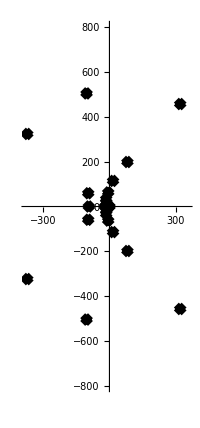

```mathematica
RootLocusPlot[1/Expand[Dc[20,x,10]],{k,0,1},FeedbackType->None]
```

```mathematica
N[Dc[20,z,20]]
```

1.+8.30161 z+7.47988 z^2+2.65334 z^3+0.501508 z^4+0.0587419 z^5+0.00464604 z^6+0.000263783 z^7+0.0000112158 z^8+3.68743×10^-7 z^9+9.62241×10^-9 z^10+2.03064×10^-10 z^11+3.52862×10^-12 z^12+5.11048×10^-14 z^13+6.24844×10^-16 z^14+6.50933×10^-18 z^15+5.82928×10^-20 z^16+4.52016×10^-22 z^17+3.05628×10^-24 z^18+1.80951×10^-26 z^19+9.44432×10^-29 z^20+4.36614×10^-31 z^21+1.78872×10^-33 z^22+6.54569×10^-36 z^23+2.1361×10^-38 z^24+6.29146×10^-41 z^25+1.67211×10^-43 z^26+3.81266×10^-46 z^27+9.4746×10^-49 z^28+8.55293×10^-52 z^29+6.02983×10^-54 z^30

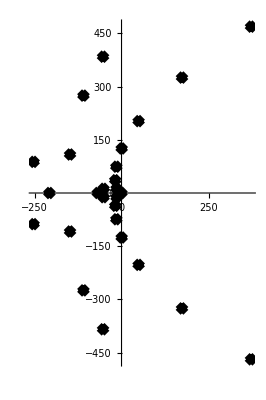

```mathematica
RootLocusPlot[1/Expand[Dc[10,x,22]],{k,0,1},FeedbackType->None]
```

```mathematica
(-1/List@@NRoots[ Dc[10,x,22]==0,x][[All,2]])
```

{0.00353273-0.00122686 ⅈ,0.00353273+0.00122686 ⅈ,0.00482654,0.00439654-0.00322286 ⅈ,0.00439654+0.00322286 ⅈ,0.00125389-0.00314563 ⅈ,0.00125389+0.00314563 ⅈ,0.0146241,0.000353284-0.00255564 ⅈ,0.000353284+0.00255564 ⅈ,0.0183872-0.00422387 ⅈ,0.0183872+0.00422387 ⅈ,0.0111077-0.0221723 ⅈ,0.0111077+0.0221723 ⅈ,0.0026152-0.012975 ⅈ,0.0026152+0.012975 ⅈ,0.0393803-0.0347825 ⅈ,0.0393803+0.0347825 ⅈ,0.111253-0.0261541 ⅈ,0.111253+0.0261541 ⅈ,0.344096,4.05819,-0.000029247-0.00797395 ⅈ,-0.000029247+0.00797395 ⅈ,-0.00113104-0.00466471 ⅈ,-0.00113104+0.00466471 ⅈ,-0.00127865-0.00239264 ⅈ,-0.00127865+0.00239264 ⅈ,-0.00103925-0.00130892 ⅈ,-0.00103925+0.00130892 ⅈ}

```mathematica
N[LogIntegral[10]-Log[Log[10]]-EulerGamma]
```

4.75435

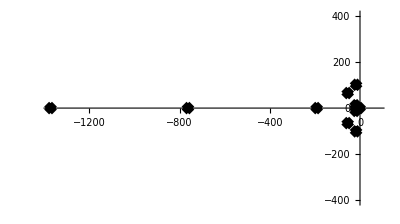

```mathematica
RootLocusPlot[1/Expand[Dc[2,x,22]],{k,0,1},FeedbackType->None]
```

```mathematica
RootLocusPlot[1/Expand[Dc[3,x,22]],{k,0,1},FeedbackType->None]
```

```mathematica
RootLocusPlot[1/Expand[Dc[4,x,22]],{k,0,1},FeedbackType->None]
```

```mathematica
RootLocusPlot[1/Expand[Dc[5,x,22]],{k,0,1},FeedbackType->None]
```

```mathematica
RootLocusPlot[1/Expand[Dc[6,x,22]],{k,0,1},FeedbackType->None]
```

```mathematica
RootLocusPlot[1/Expand[Dc[7,x,22]],{k,0,1},FeedbackType->None]
```

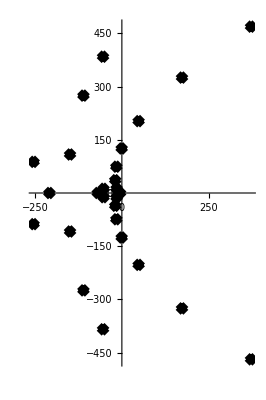

```mathematica
RootLocusPlot[1/Expand[gg[10,x,22]],{k,0,1},FeedbackType->None]
```